```mathematica
(* THREE REACTIONS: A -> A+A, A+A -> B, B -> A *)
```

```mathematica
AVOGADRO=6.0221367*10^23;
Mtoperm3[molar_]= molar*(1000*AVOGADRO);
microMtoperm3[micromolar_]= Mtoperm3[micromolar/(1*10^6)];calckD[Diffusion_,sigma_]= 4.0*Pi*Diffusion*sigma;
calcka[konvar_,kDvar_]=1/((1/konvar)-(1/kDvar));
calckd[koffvar_,konvar_,kDvar_] =calcka[konvar,kDvar]*koffvar/konvar;
```

```mathematica
NA=1.;
NB=0;
L=1*10^(-6);
VOLUME=L^3;
CONCENTRATIONA=NA / VOLUME;
CONCENTRATIONB= NB / VOLUME;
```

```mathematica
DA=1.0*10^-12;
RADIUSA=5.0*10^-9;

STARTA = CONCENTRATIONA*10;
STARTB = CONCENTRATIONB *10;

k1=10;
k2=1.*10^(-19);
k3=0.1;
kD=calckD[2*DA,2*RADIUSA];

kd=calckd[k1,k2,kD];
ka=calcka[k2,kD];

kon/koff;
ka/kd;
```

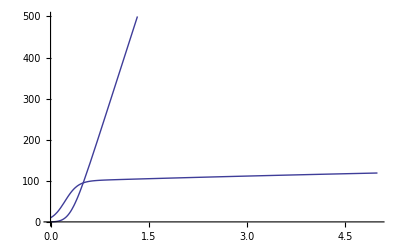

{118.966}

{2291.18}

```mathematica
ENDTIME = 5;
s = NDSolve[{
A'[t]==k1*A[t]+k3*B[t]-k2*A[t]^2,
B'[t]==k2 /2.* A[t]^2 - k3*B[t] , 
A[0]==STARTA,
B[0]==STARTB
}, {A, B}, {t, 0, ENDTIME}];
Plot[{A[t]*VOLUME, B[t]*VOLUME} /. s, {t, 0, ENDTIME},PlotRange->{0, 500}] 
A[ENDTIME]*VOLUME/.s
B[ENDTIME]*VOLUME/.s
```

```mathematica
dAdt[t_]=k1*A[t]+k3*B[t]-k2*A[t]^2;
dBdt[t_]=k2 /2.* A[t]^2 - k3*B[t] ;
m11=D[dAdt[t], A[t]]/.A[t]->CONCENTRATIONA;
m12=D[dAdt[t], B[t]];
m21 = D[dBdt[t], A[t]]/.A[t]->CONCENTRATIONA;
m22=D[dBdt[t], B[t]];
Eigenvalues[{{m11, m12}, {m21, m22}}]
```

{-544.949,-55.051}